Analisi della risposta libera (con l’uscita) per un sistema del III ordine a tempo continuo

```mathematica
A=({{-1, 0, 0}, {-1, -15/2, 17/2}, {-1, -13/2, 7/2}})
```

{{-1,0,0},{-1,-15/2,17/2},{-1,-13/2,7/2}}

Individuo i modi naturali del sistema a partire dagli autovalori della matrice dinamica

```mathematica
λ=Eigenvalues[A]
```

{-2+5 ⅈ,-2-5 ⅈ,-1}

```mathematica
σ=Re[λ[[1]]]
```

-2

```mathematica
ω=Im[λ[[1]]]
```

5

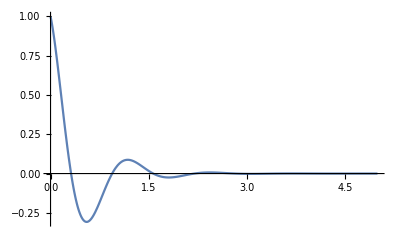

```mathematica
Plot[Exp[σ t]Cos[ω t],{t,0,5},PlotRange->All]
```

Sullo stesso grafico sovrappongo il modo pseudo-periodico con la sua componente periodica

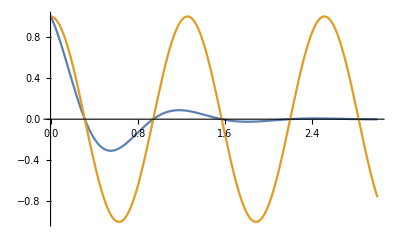

```mathematica
Plot[{Exp[σ t]Cos[ω t],Cos[ω t]},{t,0,3},PlotRange->All]
```

Mi calcolo il polinomio caratteristico di A, det(A - lambda I)

```mathematica
CharacteristicPolynomial[A,x]
```

-29-33 x-5 x^2-x^3

Genero una combinazione lineare delle potenze di A i cui coefficienti sono quelli del polinomio caratteristico

```mathematica
Simplify[A.A.A+5A.A+33 A+29 IdentityMatrix[3]]
```

{{0,0,0},{0,0,0},{0,0,0}}

Ho verificato che la matrice A annulla il proprio polinomio caratteristico (e’ sempre vero). Teorema di Cayley-Hamilton

Inserisco lo stato iniziale e lo proietto lungo le componenti della base individuata da T_tilde

```mathematica
Subscript[x, 0]={{0},{1},{-3}}
```

{{0},{1},{-3}}

```mathematica
T=Transpose[Eigenvectors[A]]
```

{{0,0,-13/2},{11/13-(10 ⅈ)/13,11/13+(10 ⅈ)/13,1},{1,1,0}}

```mathematica
MatrixForm[T]
```

(0 | 0 | -13/2
11/13-(10 ⅈ)/13 | 11/13+(10 ⅈ)/13 | 1
1 | 1 | 0)

```mathematica
T̃=Transpose[{Re[T[[All,1]]],Im[T[[All,1]]],T[[All,3]]}]
```

{{0,0,-13/2},{11/13,-10/13,1},{1,0,0}}

```mathematica
MatrixForm[T̃]
```

(0 | 0 | -13/2
11/13 | -10/13 | 1
1 | 0 | 0)

Vediamo come e’ strutturata la forma canonica di A secondo questa matrice di cambiamento di base

```mathematica
Inverse[T̃].A.T̃
```

{{-2,5,0},{-5,-2,0},{0,0,-1}}

```mathematica
MatrixForm[Inverse[T̃].A.T̃]
```

(-2 | 5 | 0
-5 | -2 | 0
0 | 0 | -1)

Mi calcolo lo stato iniziale proiettato lungo le colonne di T_tilde

```mathematica
Subscript[z, 0]=Inverse[T̃].Subscript[x, 0]
```

{{-3},{-23/5},{0}}

Vado ad immagazzinare la matrice di uscita

```mathematica
Cc=({{1, 0, -3}})
```

{{1,0,-3}}

Risposta libera nello stato

```mathematica
Subscript[x, l][t_]:=Simplify[T̃.({{Exp[σ t]Cos[ω t], Exp[σ t]Sin[ω t], 0}, {-Exp[σ t]Sin[ω t], Exp[σ t]Cos[ω t], 0}, {0, 0, Exp[λ[[3]] t]}}).Subscript[z, 0]]
```

```mathematica
Subscript[x, l][t]
```

{{0},{1/5 ⅇ^(-2 t) (5 Cos[5 t]-31 Sin[5 t])},{-1/5 ⅇ^(-2 t) (15 Cos[5 t]+23 Sin[5 t])}}

```mathematica
MatrixForm[Subscript[x, l][t]]
```

(0
1/5 ⅇ^(-2 t) (5 Cos[5 t]-31 Sin[5 t])
-1/5 ⅇ^(-2 t) (15 Cos[5 t]+23 Sin[5 t]))

```mathematica
MatrixForm[Subscript[x, 0]]
```

(0
1
-3)

```mathematica
MatrixForm[T̃]
```

(0 | 0 | -13/2
11/13 | -10/13 | 1
1 | 0 | 0)

```mathematica
Subscript[y, l][t_]:=Cc.Subscript[x, l][t]
```

```mathematica
Subscript[y, l][t]
```

{{3/5 ⅇ^(-2 t) (15 Cos[5 t]+23 Sin[5 t])}}

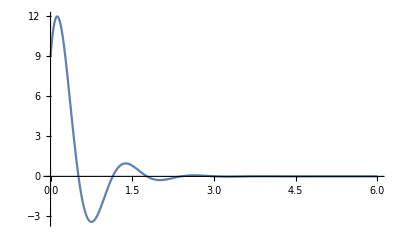

```mathematica
Plot[Subscript[y, l][t],{t,0,6},PlotRange->All]
```

Cambio lo stato iniziale in maniera tale da “accendere” tutti e tre i modi naturali del sistema

```mathematica
Subscript[x, 0]={{1},{1},{1}}
```

{{1},{1},{1}}

```mathematica
Subscript[z, 0]=Inverse[T̃].Subscript[x, 0]
```

{{1},{-2/5},{-2/13}}

```mathematica
Subscript[x, l][t_]:=Simplify[T̃.({{Exp[σ t]Cos[ω t], Exp[σ t]Sin[ω t], 0}, {-Exp[σ t]Sin[ω t], Exp[σ t]Cos[ω t], 0}, {0, 0, Exp[λ[[3]] t]}}).Subscript[z, 0]]
```

```mathematica
MatrixForm[Subscript[x, l][t]]
```

(ⅇ^-t
1/65 ⅇ^(-2 t) (-10 ⅇ^t+75 Cos[5 t]+28 Sin[5 t])
1/5 ⅇ^(-2 t) (5 Cos[5 t]-2 Sin[5 t]))

```mathematica
Subscript[y, l][t_]:=Cc.Subscript[x, l][t]
```

```mathematica
Subscript[y, l][t]
```

{{ⅇ^-t-3/5 ⅇ^(-2 t) (5 Cos[5 t]-2 Sin[5 t])}}

Come dovrebbe essere strutturata la matrice di uscita C per fare in modo che soltanto il modo naturale esponenziale sia presente.

```mathematica
MatrixForm[T̃]
```

(0 | 0 | -13/2
11/13 | -10/13 | 1
1 | 0 | 0)

```mathematica
Subscript[Cc, 1]=({{1, 0, 0}})
```

{{1,0,0}}

```mathematica
Subscript[y, l1][t_]:=Subscript[Cc, 1].Subscript[x, l][t]
```

```mathematica
Subscript[y, l1][t]
```

{{ⅇ^-t}}

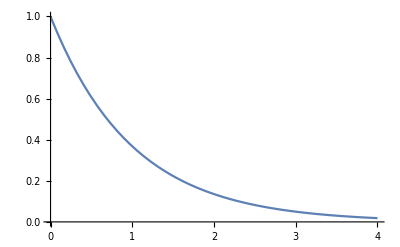

```mathematica
Plot[Subscript[y, l1][t],{t,0,4}]
```

Desidero graficare la risposta libera nel caso di matrice di uscita generica

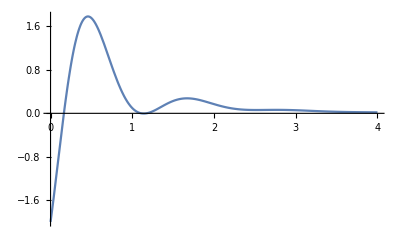

```mathematica
Plot[Subscript[y, l][t],{t,0,4},PlotRange->All]
```

Per comprendere il concetto di dominanza, rappresentiamo sullo stesso grafico l’esponenziale legato al modo reale e l’esponenziale legato ai modi pseudo-periodici

```mathematica
Plot[{Exp[-t],Exp[-2t]},{t,0,4},PlotRange->All,PlotLabels->{"Exp[-t]","Exp[-2 t]"}]
```

-Graphics-

```mathematica
N[1/Exp[1]]
```

0.367879